# Pascal’s Triangle Fractals

Adam Rumpf, 6/28/2015

## Introduction

This Notebook contains a variety of functions for generating graphics of Pascal’s triangle. The pascal[] function simply displays Pascal’s triangle with a specified number of rows and with the numbers filled in. The parity[] function accepts arguments for a number of rows and a base, and displays Pascal’s triangle colored so that the entries divisible by the chosen base are blank while the rest are black.

The main motivation for these functions is to see the fractal structures present in Pascal’s triangle. Speficically, highlighting only the odd entries creates a Sierpiński triangle. This corresponds to using the above parity[] function with a base of 2. Other choices of base generate different fractals.

## Code

### Initialization

```mathematica
(* Displays Pascal's triangle (with numbers) for a specified number of rows. *)
pascal[n_]:=Module[{g={},pt,tab=ConstantArray[Null,{n,n}]},
For[i=0,i<n,i++,
For[j=0,j≤i,j++,
tab[[i+1,j+1]]=Binomial[i,j];
];
];
For[i=1,i≤Length[tab],i++,
For[j=1,j≤i,j++,
pt={-0.5i+j-1,-√3 i/2};
g=Join[g,{Circle[pt,0.5],Style[Text[tab[[i,j]],pt],20]}];
];
];
Show[Graphics[g]]
]
```

```mathematica
(* Displays a colored version of Pascal's triangle (with no numbers) for a specified number of rows and a specified base. Elements divisible by the base are left blank, while all remaining elements are colored in. *)
parity[n_,p_]:=Module[{g={},pt,tab=ConstantArray[Null,{n,n}]},
For[i=0,i<n,i++,
For[j=0,j≤i,j++,
tab[[i+1,j+1]]=Binomial[i,j];
];
];
For[i=1,i≤Length[tab],i++,
For[j=1,j≤i,j++,
pt={-0.5i+j-1,-√3 i/2};
g=Join[g,{If[Mod[tab[[i,j]],p]==0,White,Black],Disk[pt,0.5]}];
];
];
Show[Graphics[g]]
]
```

### Demonstration

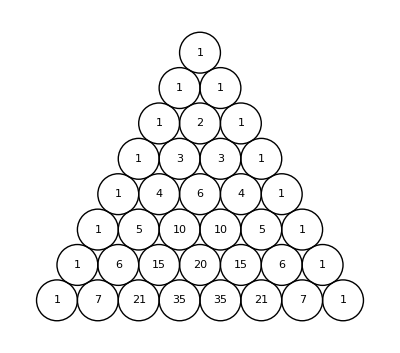

```mathematica
(* Display 10 rows of Pascal's triangle. *)
pascal[8]
```

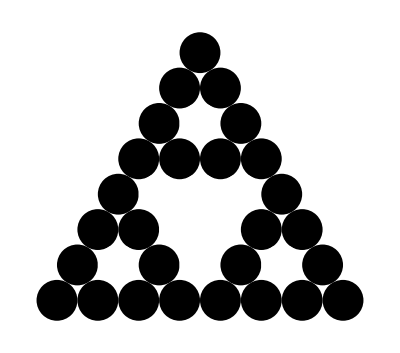

```mathematica
(* Same as above, but coloring odd entries. *)
parity[8,2]
```

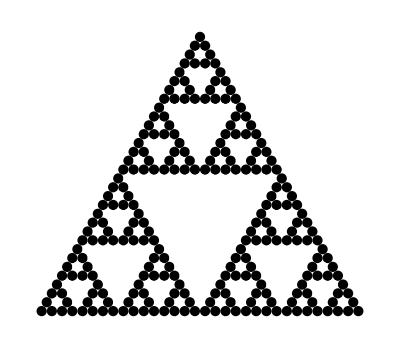

```mathematica
(* Zooming out. *)
parity[32,2]
```

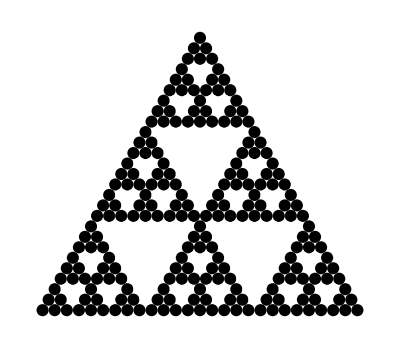

```mathematica
(* Base 3. *)
parity[27,3]
```

```mathematica
(* Manipulate version of the above. *)
Manipulate[parity[32,p],{{p,2,"base"},2,12,1}]
```